```mathematica
theorydata={#1,10^-3#2}&@@@Import[NotebookDirectory[]<>"Singlet-VLL-theory.csv"]
```

{{157.143,0.180729},{211.887,0.0716839},{277.714,0.026405},{343.632,0.0104732},{420.901,0.00481649},{498.082,0.00205709},{586.525,0.000946027},{675.013,0.000451459},{796.841,0.000185813},{952.099,0.0000710241},{1074.11,0.0000338938},{1185.12,0.0000187539},{1285.01,0.0000107678}}

```mathematica
observedata=Import[NotebookDirectory[]<>"VLL-observe.csv"]
```

{{124.885,5.2922},{137.327,1.93764},{149.77,0.784414},{176.728,0.474639},{209.908,0.277739},{247.235,0.168056},{292.857,0.105152},{346.774,0.0538157},{396.544,0.0304534},{446.313,0.0166655},{494.009,0.0107827},{550.,0.00797661},{620.507,0.0053367},{670.276,0.00436516},{742.857,0.00381784},{815.438,0.00345288},{890.092,0.00292048},{960.599,0.0026413},{997.926,0.0026413}}

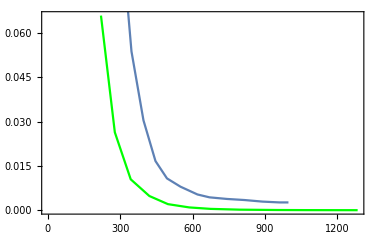

```mathematica
Show[ListLinePlot[theorydata,PlotStyle->Green],ListLinePlot[observedata]]
```